## Setup

Requirements:
At least Mathematica 8.0.4 is necessary for this package.

load the supplied package

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<CauchyIntegral`
```

## Basic Example

To calculate the derivative of a function using Cauchy’s integral formula this package provides the function CauchyIntegralD. CauchyIntegralD[f,z,n] tries to numerically calculate the n-th derivative of f at z.
For example to calculate the 20-th derivative of the e function at z=0 we could use the following command.

```mathematica
CauchyIntegralD[Exp,20,0]
```

1.+5.35998×10^-17 ⅈ

## Detailed Example

This example gives some more details about the steps done by CauchyIntegralD to calculate the derivative of a function. At first we define a more complicated test function.

```mathematica
f[z_] := Exp[-1/(1+8 z)^5](1-z)^(11/2)BesselJ[0,z]
```

Now we can calculate an suitable contour which yields a small condition number for the Cauchy integral, e.g. for z=1/√2 and n = 100. This is done by the function CauchyIntegralSEW. As f has a branch-cut we have to specify it with the option “Cuts” so that the algorithm removes edges crossing this line from the graph. In addition we specify an additional cut from the left border to the essential singularity. This prevents the SEW from enclosing the essential singularity.

```mathematica
n=100;
z=1/Sqrt[2];
{g,sew}=CauchyIntegralSEW[f,n,z,
"Cuts"->{Line[{1,100}],Line[{-100,-0.125}]}
];
```

To visualize the just calculated contour, we use SEWContourPlot to create a contour plot of the weight of the vertices in the graph g. The color encodes the weight of the vertices in g; with w̄ being the maximum weight of a vertex in the SEW, yellow corresponds to w̄, red is 10^16 w̄ and green ist 10^-16 w̄. The blue line is the SEW.

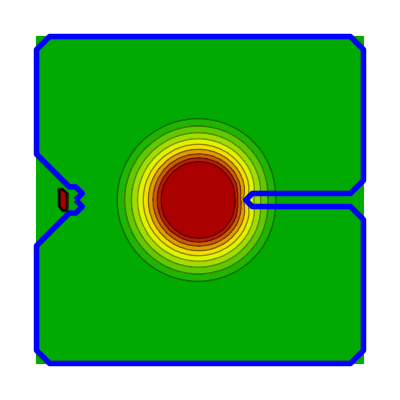

```mathematica
SEWContourPlot[g,sew]
```

Finally we evaluate the Cauchy integral along the SEW.

```mathematica
CauchyIntegral[g,sew,f,n,z]
```

1.93144×10^197-7.8147×10^184 ⅈ

## Options

The following options are available for CauchyIntegralD.

### “Cuts”

Specifies lines along which the graphs created to calculate the SEW should be cut.

### WorkingPrecision

Sets the precision used for calculating the SEW and evaluating the integral. Default: MachinePrecision

### PrecisionGoal

Sets the precision we want to achieve for the approximaion of the integral value. Default: MachinePrecision

### “GridSize”

Number of vertices in x and y direction; the default value of 51 yields grids with 51x51 vertices.

### “InitialGridRadius”

Sets the radius of the first grid that is used to calculate a SEW. The default value is 1 and will yield a first grid that covers the square defined by the two points (-1,-1) and (1,1).

### “MaxGridRadius”

Sets the maximum radius that a grids used to calculate a SEW may have. If CauchyIntegralD reaches this value, it will abort and return the best SEW it has found so far.
If “MaxGridRadius” = “InitialGridRadius” CauchyIntegralD will only caluclate the SEW in a grid with the specified radius.